```mathematica
{vf, vars,descr,kd}=DarbouxBench[[1]];

matringe=DarbouxPolyGen`MatringeCompleteDbx[2,vf,vars]
```

6

5

Minimised rank is 5. Returning all solutions:

{{COFACTCOEFF1→6,COFACTCOEFF2→0,COFACTCOEFF3→-12},{COFACTCOEFF1→3,COFACTCOEFF2→0,COFACTCOEFF3→-6},{COFACTCOEFF1→0,COFACTCOEFF2→0,COFACTCOEFF3→0},{COFACTCOEFF1→6,COFACTCOEFF2→0,COFACTCOEFF3→0},{COFACTCOEFF1→3,COFACTCOEFF2→0,COFACTCOEFF3→6},{COFACTCOEFF1→6,COFACTCOEFF2→0,COFACTCOEFF3→12}}

{-4-4 x-x^2,2+x,1,-4+x^2,-2+x,-4+4 x-x^2}

```mathematica
naive=DarbouxPolyGen`DbxNaive[2,vf,vars]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{2+x,-2+x}

```mathematica
manps1=DarbouxPolyGen`ManPS1[2,vf,vars]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{-2+x,2+x}

```mathematica
manps2=DarbouxPolyGen`ManPS2[2,vf,vars]
```

{-2+x,2+x}

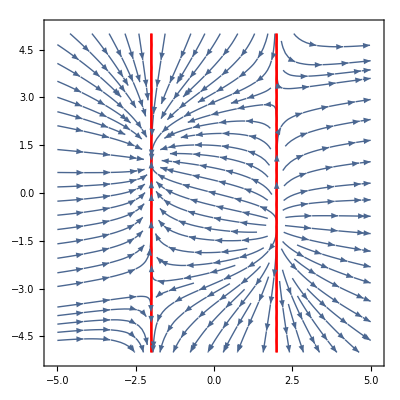

```mathematica
scale=5;
Show[
StreamPlot[vf, {x,-scale,scale},{y,-scale,scale}],
ContourPlot[matringe==0,{x,-scale,scale},{y,-scale,scale},ContourStyle->Red]
]
```